# Newtonsche Interpolationsformel

### Ausgangslage

```mathematica
f[x_]:=E^(Cos[x]^2)
```

```mathematica
pts=Table[{x,f[x]},{x,1,5,0.5}]
```

{{1.,1.339},{1.5,1.00502},{2.,1.18908},{2.5,1.89996},{3.,2.66468},{3.5,2.40356},{4.,1.53304},{4.5,1.04544},{5.,1.08379}}

```mathematica
m=Length[pts]
```

9

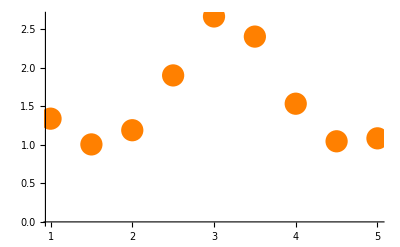

```mathematica
plpts=ListPlot[pts,PlotStyle->{Orange,PointSize[.04]}]
```

## Polynom Interpolation

```mathematica
polys[x_]=Table[InterpolatingPolynomial[pts[[;;k]],x],{k,1,m}]//Simplify;
```

```mathematica
polys[x]//Expand//TableForm
```

1.339
2.00698-0.667977 x
3.56113-3.25823 x+1.0361 x^2
3.52606-3.18225 x+0.983498 x^2+0.0116893 x^3
1.11738+3.00004 x-4.71705 x^2+2.25979 x^3-0.321158 x^4
1.86733+0.825189 x-2.30055 x^2+0.968217 x^3+0.0121523 x^4-0.033331 x^5
17.4624-48.8562 x+60.8717 x^2-40.2472 x^3+14.617 x^4-2.70677 x^5+0.198032 x^6
59.4704-193.184 x+264.494 x^2-193.81 x^3+81.7131 x^4-19.7433 x^5+2.53181 x^6-0.133359 x^7
129.393-448.957 x+656.812 x^2-524.735 x^3+250.197 x^4-72.9193 x^5+12.7181 x^6-1.21858 x^7+0.0493284 x^8

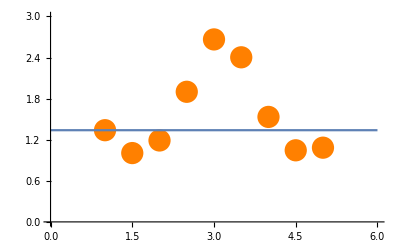
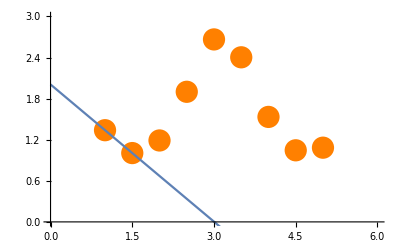
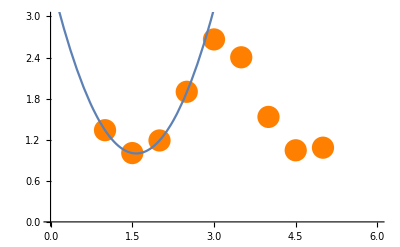
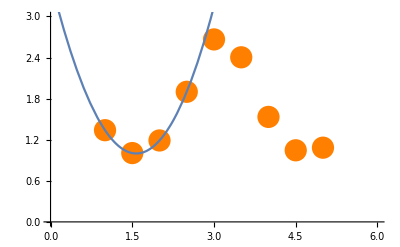
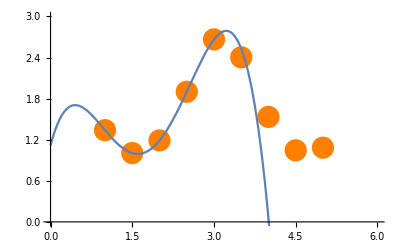
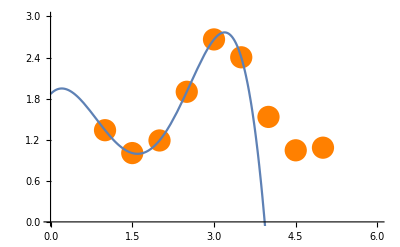
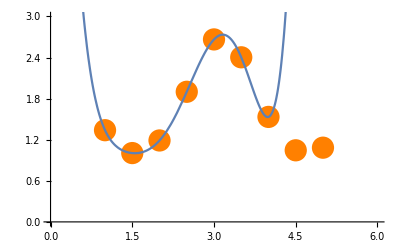
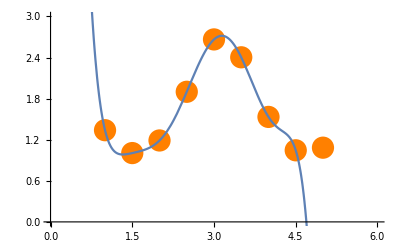

```mathematica
Table[Show[plpts,Plot[polys[x][[k]],{x,0,6}],PlotRange->{{0,6},{0,3}},AxesOrigin->{0,0}],{k,1,m}]
```

```mathematica
corrector[x_,n_]:=(pts[[n,2]]-polys[pts[[n,1]]][[n-1]])/Product[pts[[n,1]]-pts[[j,1]],{j,1,n-1}] Product[x-pts[[j,1]],{j,1,n-1}]
```

```mathematica
Table[corrector[x,k+1]//Expand,{k,1,m-1}]//TableForm
```

0.667977-0.667977 x
1.55415-2.59025 x+1.0361 x^2
-0.0350678+0.0759803 x-0.0526017 x^2+0.0116893 x^3
-2.40868+6.18228 x-5.70055 x^2+2.2481 x^3-0.321158 x^4
0.749947-2.17485 x+2.4165 x^2-1.29158 x^3+0.33331 x^4-0.033331 x^5
15.595-49.6813 x+63.1723 x^2-41.2155 x^3+14.6049 x^4-2.67344 x^5+0.198032 x^6
42.008-144.327 x+203.622 x^2-153.563 x^3+67.0961 x^4-17.0366 x^5+2.33378 x^6-0.133359 x^7
69.923-255.774 x+392.318 x^2-330.926 x^3+168.484 x^4-53.176 x^5+10.1863 x^6-1.08522 x^7+0.0493284 x^8

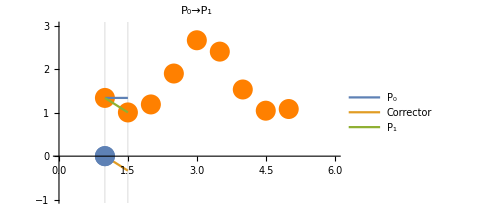
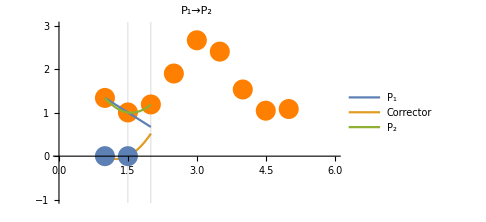
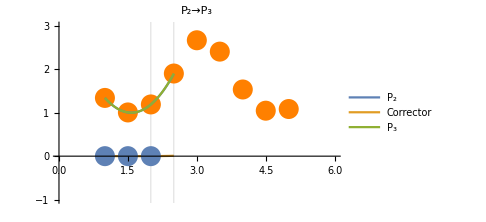
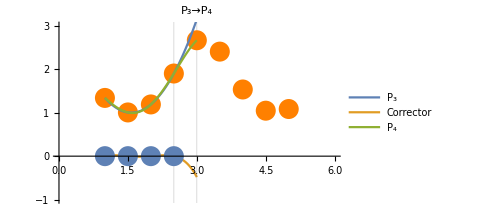
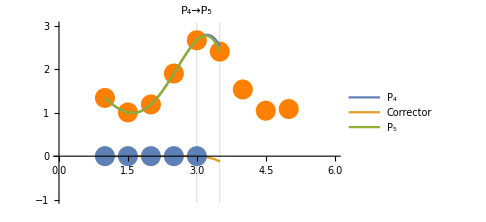
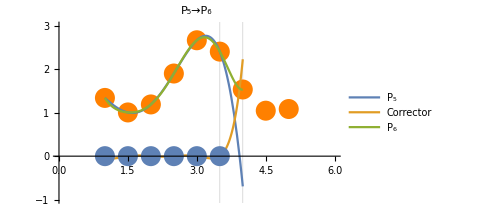
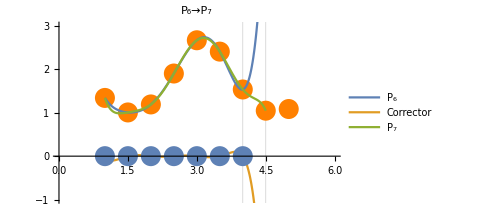
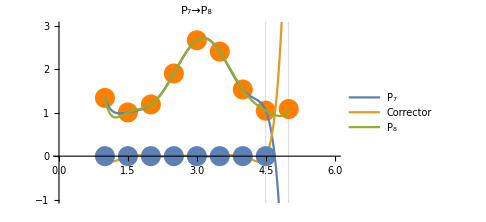

```mathematica
Table[Show[plpts,Plot[{polys[x][[k]],corrector[x,k+1],polys[x][[k]]+corrector[x,k+1]},{x,pts[[1,1]],pts[[k+1,1]]},PlotStyle->Thick,PlotLegends->{ToString[Subscript["P",k-1],TraditionalForm],"Corrector",ToString[Subscript["P",k],TraditionalForm]}],ListPlot[Table[{pts[[j,1]],0},{j,1,k}],PlotStyle->PointSize[.04]],PlotRange->{{0,6},{-1,3}},AxesOrigin->{0,0},GridLines->{{pts[[k,1]],pts[[k+1,1]]},None},ImageSize->Medium,PlotLabel->ToString[Subscript["P",k-1],TraditionalForm]<>"→"<>ToString[Subscript["P",k],TraditionalForm]],{k,1,m-1}]
```

#### Kontrolle P_k+Corrector = P_(k+1)

Differenz sollte Null sein:

```mathematica
Table[polys[x][[k]]+corrector[x,k+1]-polys[x][[k+1]],{k,1,m-1}]
```

{-0.667977-0.667977 (-1.+x)+0.667977 x,-1.55415+1.0361 (-1.5+x) (-1.+x)+2.59025 x-1.0361 x^2,0.0350678+0.0116893 (-2.+x) (-1.5+x) (-1.+x)-0.0759803 x+0.0526017 x^2-0.0116893 x^3,2.40868-0.321158 (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)-6.18228 x+5.70055 x^2-2.2481 x^3+0.321158 x^4,-0.749947-0.033331 (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)+2.17485 x-2.4165 x^2+1.29158 x^3-0.33331 x^4+0.033331 x^5,-15.595+0.198032 (-3.5+x) (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)+49.6813 x-63.1723 x^2+41.2155 x^3-14.6049 x^4+2.67344 x^5-0.198032 x^6,-42.008-0.133359 (-4.+x) (-3.5+x) (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)+144.327 x-203.622 x^2+153.563 x^3-67.0961 x^4+17.0366 x^5-2.33378 x^6+0.133359 x^7,-69.923+0.0493284 (-4.5+x) (-4.+x) (-3.5+x) (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)+255.774 x-392.318 x^2+330.926 x^3-168.484 x^4+53.176 x^5-10.1863 x^6+1.08522 x^7-0.0493284 x^8}

```mathematica
%//Simplify
```

{0.,2.22045×10^-16+4.44089×10^-16 x,-6.21725×10^-15+1.27259×10^-14 x-8.6528×10^-15 x^2+1.92381×10^-15 x^3,8.88178×10^-16 (-2.+1. x)^3 (-1.+1. x),-7.77156×10^-16+6.21725×10^-15 x-1.15463×10^-14 x^2+8.88178×10^-15 x^3-2.94209×10^-15 x^4+3.53884×10^-16 x^5,-1.1191×10^-13+3.41061×10^-13 x-4.12115×10^-13 x^2+2.55795×10^-13 x^3-8.70415×10^-14 x^4+1.5099×10^-14 x^5-1.05471×10^-15 x^6,5.81935×10^-12-2.00089×10^-11 x+2.82228×10^-11 x^2-2.13163×10^-11 x^3+9.2939×10^-12 x^4-2.36611×10^-12 x^5+3.23297×10^-13 x^6-1.8513×10^-14 x^7,-1.32616×10^-10+4.85073×10^-10 x-7.44194×10^-10 x^2+6.27836×10^-10 x^3-3.19631×10^-10 x^4+1.00897×10^-10 x^5-1.93321×10^-11 x^6+2.05969×10^-12 x^7-9.36265×10^-14 x^8}

Bis auf den numerischen Fehler passt das:

```mathematica
%//Chop
```

{0,0,0,0,0,0,0,-1.32616×10^-10+4.85073×10^-10 x-7.44194×10^-10 x^2+6.27836×10^-10 x^3-3.19631×10^-10 x^4+1.00897×10^-10 x^5}

## Praktische Umsetzung, Rechenschema